```mathematica
Sum[1/(2*i + 1)^2, {i, -Infinity, Infinity}]
```

π^2/4

WolframAlphaQueryParseResults

{nitrogen,iodine,phosphorus}

Sum[Log[k^2 + 5^k + 6], k]

WolframAlphaQueryResults

Sum[Log[k^2 + 5^k + 6], k]

```mathematica
Sum[Log[k^2 + 5^k + 6], k > 0]
```

Sum::vloc: The variable k>0 cannot be localized so that it can be assigned to numerical values.

∑_(k>0) Log[k^2+5^k+6]

```mathematica
Sum[x^n, {n, 0, Infinity}, GenerateConditions-> True]
```

ConditionalExpression[1/(1-x), Abs[x]<1]

```mathematica
Sum[1 / (k + a)^ 2, {k, 0, Infinity},
GenerateConditions->True]
```

ConditionalExpression[PolyGamma[1,a], a[Notplayplus]ℤ||Im[a]≠0||a>0]

```mathematica
Entity["Word","array"][EntityProperty["Word","Definitions"]]
```

{{array,Noun,Arrangement}→an orderly arrangement,{array,Noun,Display}→an impressive display,{array,Noun,Wearable}→especially fine or decorative clothing,{array,Noun,DirectionalAntenna}→an arrangement of aerials spaced to give desired directional characteristics,{array,Verb,SetUp}→lay out orderly or logically in a line or as if in a line,{array,Verb,Stand}→align oneself with a group or a way of thinking}

WolframAlphaQueryParseResults

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27}

```mathematica
Range[1.2, 1.2, 27]
```

{1.2}

```mathematica
Range[x, x + 4]
```

{x,1+x,2+x,3+x,4+x}

```mathematica
Range[a, b, (b - a) / 4]
```

{a,a+1/4 (-a+b),a+1/2 (-a+b),a+3/4 (-a+b),b}

```mathematica
Range[a, b, (b - a) / Sum[a, 10]]
```

Range::range: Range specification in Range[a,b,(-a+b)/(∑_10 a)] does not have appropriate bounds.

Range[a,b,(-a+b)/(∑_10 a)]

Range[a,b,(-a+b)/(∑_10 a)]

It looks like you're working with a variety of tasks involving summation, range generation, and entities. Let's address some key points from your inputs:

1. Summation: 
   • The expression Sum[Log[k^2 + 5^k + 6], k] you queried returns that the sum diverges. This means that the series does not converge to a finite value.
   • When using Sumpaclet:ref/Sumhttps://reference.wolfram.com/language/ref/Sum.html in Wolfram Language, ensure that the iterator is specified correctly. For example, Sum[Log[k^2 + 5^k + 6], {k, 1, Infinity}] is the correct syntax for an infinite series starting from .
2. Range: 
   • When using Rangepaclet:ref/Rangehttps://reference.wolfram.com/language/ref/Range.html, the syntax is Range[start, stop, step]. If step isn't specified, it defaults to 1.
   • In your example Range[a, b, (b - a) / Sum[a, 10]], the Sum[a, 10] part seems incorrect as a step size. This should be a numerical value.
   • The Wolfram Language error message Range::range indicates that the range specification isn't valid. Make sure start, stop, and step are properly defined.
3. Entities: 
   • The entity syntax like Entity["playplus", "Nitrogen"] is used to represent specific entities, similar to chemical elements or other well-defined objects. Ensure the correct use of entities based on their context.
If you need further clarification or a specific task addressed, feel free to ask!

WolframAlphaQueryResults

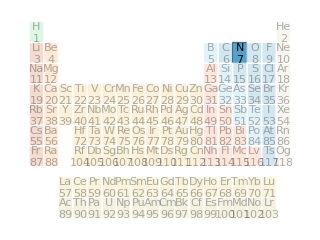

```mathematica
q ^ Range[4]
```

{q,q^2,q^3,q^4}

WolframAlphaQueryParseResults

{q/2,q^2/2,q^3/2,q^4/2}

```mathematica
RandomSample[q^ Range[10]]
```

{q^10,q^5,q^7,q,q^9,q^2,q^4,q^3,q^6,q^8}

```mathematica
l1 = RandomSample[Range[10]]
```

{10,2,3,9,6,1,5,4,7,8}

```mathematica
Range[Length[l1]]
```

```mathematica
{1,2,3,4,5,6,7,8,9,10}
```

{1,2,3,4,5,6,7,8,9,10}

WolframAlphaQueryParseResults

Range::argb: Range called with 4 arguments; between 1 and 3 arguments are expected.

Range[4,2,0,9]

WolframAlphaQueryParseResults

{4,7}

WolframAlphaQueryParseResults

False

```mathematica
{HoldComplete[{1 ;; 5 ;; 2}]}
```

{HoldComplete[{1;;5;;2}]}

```mathematica
Range[Range[12]]
```

{{1},{1,2},{1,2,3},{1,2,3,4},{1,2,3,4,5},{1,2,3,4,5,6},{1,2,3,4,5,6,7},{1,2,3,4,5,6,7,8},{1,2,3,4,5,6,7,8,9},{1,2,3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8,9,10,11},{1,2,3,4,5,6,7,8,9,10,11,12}}

```mathematica
Range[Range[Range[22]]]
```

{{{1}},{{1},{1,2}},{{1},{1,2},{1,2,3}},{{1},{1,2},{1,2,3},{1,2,3,4}},{{1},{1,2},{1,2,3},{1,2,3,4},{1,2,3,4,5}},{{1},{1,2},{1,2,3},{1,2,3,4},{1,2,3,4,5},{1,2,3,4,5,6}},{{1},{1,2},{1,2,3},{1,2,3,4},{1,2,3,4,5},{1,2,3,4,5,6},{1,2,3,4,5,6,7}},{{1},{1,2},{1,2,3},{1,2,3,4},{1,2,3,4,5},{1,2,3,4,5,6},{1,2,3,4,5,6,7},{1,2,3,4,5,6,7,8}},{{1},{1,2},{1,2,3},{1,2,3,4},{1,2,3,4,5},{1,2,3,4,5,6},{1,2,3,4,5,6,7},{1,2,3,4,5,6,7,8},{1,2,3,4,5,6,7,8,9}},{{1},{1,2},{1,2,3},{1,2,3,4},{1,2,3,4,5},{1,2,3,4,5,6},{1,2,3,4,5,6,7},{1,2,3,4,5,6,7,8},{1,2,3,4,5,6,7,8,9},{1,2,3,4,5,6,7,8,9,10}},{{1},{1,2},{1,2,3},{1,2,3,4},{1,2,3,4,5},{1,2,3,4,5,6},{1,2,3,4,5,6,7},{1,2,3,4,5,6,7,8},{1,2,3,4,5,6,7,8,9},{1,2,3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8,9,10,11}},{{1},{1,2},{1,2,3},{1,2,3,4},{1,2,3,4,5},{1,2,3,4,5,6},{1,2,3,4,5,6,7},{1,2,3,4,5,6,7,8},{1,2,3,4,5,6,7,8,9},{1,2,3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8,9,10,11},{1,2,3,4,5,6,7,8,9,10,11,12}},{{1},{1,2},{1,2,3},{1,2,3,4},{1,2,3,4,5},{1,2,3,4,5,6},{1,2,3,4,5,6,7},{1,2,3,4,5,6,7,8},{1,2,3,4,5,6,7,8,9},{1,2,3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8,9,10,11},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12,13}},{{1},{1,2},{1,2,3},{1,2,3,4},{1,2,3,4,5},{1,2,3,4,5,6},{1,2,3,4,5,6,7},{1,2,3,4,5,6,7,8},{1,2,3,4,5,6,7,8,9},{1,2,3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8,9,10,11},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12,13},{1,2,3,4,5,6,7,8,9,10,11,12,13,14}},{{1},{1,2},{1,2,3},{1,2,3,4},{1,2,3,4,5},{1,2,3,4,5,6},{1,2,3,4,5,6,7},{1,2,3,4,5,6,7,8},{1,2,3,4,5,6,7,8,9},{1,2,3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8,9,10,11},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12,13},{1,2,3,4,5,6,7,8,9,10,11,12,13,14},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15}},{{1},{1,2},{1,2,3},{1,2,3,4},{1,2,3,4,5},{1,2,3,4,5,6},{1,2,3,4,5,6,7},{1,2,3,4,5,6,7,8},{1,2,3,4,5,6,7,8,9},{1,2,3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8,9,10,11},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12,13},{1,2,3,4,5,6,7,8,9,10,11,12,13,14},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16}},{{1},{1,2},{1,2,3},{1,2,3,4},{1,2,3,4,5},{1,2,3,4,5,6},{1,2,3,4,5,6,7},{1,2,3,4,5,6,7,8},{1,2,3,4,5,6,7,8,9},{1,2,3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8,9,10,11},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12,13},{1,2,3,4,5,6,7,8,9,10,11,12,13,14},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17}},{{1},{1,2},{1,2,3},{1,2,3,4},{1,2,3,4,5},{1,2,3,4,5,6},{1,2,3,4,5,6,7},{1,2,3,4,5,6,7,8},{1,2,3,4,5,6,7,8,9},{1,2,3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8,9,10,11},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12,13},{1,2,3,4,5,6,7,8,9,10,11,12,13,14},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18}},{{1},{1,2},{1,2,3},{1,2,3,4},{1,2,3,4,5},{1,2,3,4,5,6},{1,2,3,4,5,6,7},{1,2,3,4,5,6,7,8},{1,2,3,4,5,6,7,8,9},{1,2,3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8,9,10,11},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12,13},{1,2,3,4,5,6,7,8,9,10,11,12,13,14},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19}},{{1},{1,2},{1,2,3},{1,2,3,4},{1,2,3,4,5},{1,2,3,4,5,6},{1,2,3,4,5,6,7},{1,2,3,4,5,6,7,8},{1,2,3,4,5,6,7,8,9},{1,2,3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8,9,10,11},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12,13},{1,2,3,4,5,6,7,8,9,10,11,12,13,14},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}},{{1},{1,2},{1,2,3},{1,2,3,4},{1,2,3,4,5},{1,2,3,4,5,6},{1,2,3,4,5,6,7},{1,2,3,4,5,6,7,8},{1,2,3,4,5,6,7,8,9},{1,2,3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8,9,10,11},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12,13},{1,2,3,4,5,6,7,8,9,10,11,12,13,14},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21}},{{1},{1,2},{1,2,3},{1,2,3,4},{1,2,3,4,5},{1,2,3,4,5,6},{1,2,3,4,5,6,7},{1,2,3,4,5,6,7,8},{1,2,3,4,5,6,7,8,9},{1,2,3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8,9,10,11},{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12,13},{1,2,3,4,5,6,7,8,9,10,11,12,13,14},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22}}}

```mathematica
ConstantArray[c, 10]
```

{c,c,c,c,c,c,c,c,c,c}

{c, c, c, c, c, c, c, c, c, c}

You're working with several operations involving ranges, entities, and lists. Here are some clarifications and suggestions based on your inputs:

1. Entities:  
   • In Wolfram Language, entities like Entity["playplus", "Nitrogen"] are used to represent specific objects or items. The image you provided shows an entity for nitrogen. You can use entities to access properties, such as their periodic table location.
2. Range and List Operations: 
   • The operation q ^ Range[4] computes powers of q from 1 to 4, producing a list: {q, q^2, q^3, q^4}.
   • The command Range[4, 2, 0, 9] results in an error because Rangepaclet:ref/Rangehttps://reference.wolfram.com/language/ref/Range.html expects 1 to 3 arguments, not 4. The syntax should be Range[start, stop, step].
   • Using Table[i, {i, 4, 9, 3}] generates numbers starting from 4, increasing by 3 until reaching or surpassing 9: {4, 7}.
   • The expression list = {a, b, c, d, e} initializes a list. Checking equality with (% == {a, b, c, d, e}) returns Falsepaclet:ref/Falsehttps://reference.wolfram.com/language/ref/False.html because % refers to the previous output, not list.
   • The command Range[Range[12]] produces nested lists, each containing sequences from 1 up to the numbers from the outer range.
   • Similarly, Range[Range[Range[22]]] generates more deeply nested lists.
3. Constant Array: 
   • The command ConstantArray[c, 10] generates a list containing the value c repeated 10 times: {c, c, c, c, c, c, c, c, c, c}.
If you have specific questions about any of these operations or need further assistance, feel free to ask!

```mathematica
Entity["MathWorld","Module"][EntityProperty["MathWorld","BasicDefinitions"]]
```

{A module is a generalization of a vector space in which the scalars form a ring rather than a field.}

```mathematica
cold = esteps[Function[{t,x},1/(t+x^2)],1,.01,100]
```

esteps[Function[{t,x},1/(t+x^2)],1,0.01,100]

```mathematica
l^2 == RandomInteger[9, 20]
```

l^2=={6,9,0,0,8,6,3,5,9,1,1,4,7,5,2,1,5,1,5,9}

```mathematica
Sum[l^2, {l1}]
```

10 l^2

WolframAlphaQueryResults